```mathematica
(* A term (final!)*)
Integrate[Exp[I x (s1 s2 - s1)]s1,{s1, 0,1},{s2,0,1}]
```

(1-ⅈ x-Cos[x]+ⅈ Sin[x])/x^2

```mathematica
(* B Term (final!) *)
Integrate[Exp[I x (s1 s2 - s2)](1-s1),{s1, 0,1},{s2,0,1}]
```

```mathematica
-(-1+ⅇ^(-ⅈ x)+ⅈ x)/x^2
```

```mathematica
(* E term (final!)*)
Integrate[Exp[I x (s1 -s1 s2)]s1 ,{s1,0,1},{s2,0,1}]
```

(1-ⅇ^(ⅈ x)+ⅈ x)/x^2

```mathematica
(* F Term (final!)*)
Integrate[Exp[I x (s2 - s1 s2)](1- s1),{s1,0,1}, {s2,0,1}]
```

(1-ⅇ^(ⅈ x)+ⅈ x)/x^2

```mathematica
(* C Term (final!)*)
Integrate[Exp[I x (s1 + s2 - 1)],{s1,0,1},{s2,0,1}]
```

(2-2 Cos[x])/x^2

transition at gamma = ds:0.

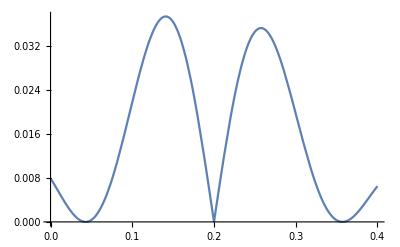

```mathematica
beta = 1;
ds = 0.2;
t = 40;
f[gamma_]:= (4 Sin[(ds - gamma)t/2]^2)/((ds - gamma)^2 t^2)Abs[1 - Exp[beta(ds - gamma)]]
Print["transition at gamma = ds: ", Limit[f[x],{x->ds}]]
Plot[f[x],{x,0,.4}]
```